# Modelo versión 3

## Análisis de pruebas realizadas anteriormente

## Importación de la red:

Pasar a SetDirectory el directorio en donde se encuentra el archivo .graphml para facilidad

Tener en cuenta que i debe cumplir con los valores de num-people

```mathematica
SetDirectory[NotebookDirectory[]];
```

# Modelo versión 3

Lim-capacity: [1-10] --> 1

## Capacidad fija

```mathematica
networks100Fixed=Table[Import[StringJoin["graphs/model-v3/fixed-t1000-2/","network-100-",IntegerString[i],".graphml"]],{i,1,10,1}];
```

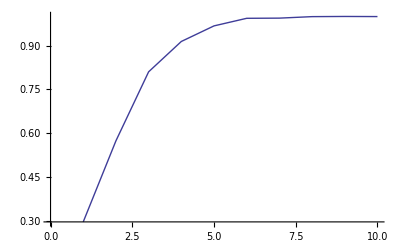

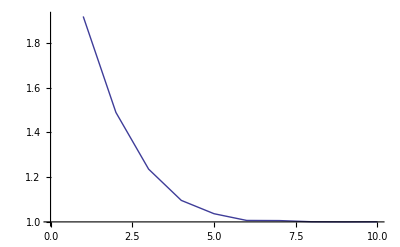

```mathematica
clustering100Fixed=Map[GlobalClusteringCoefficient,networks100Fixed];
apl100Fixed=Map[MeanGraphDistance,networks100Fixed];
ListPlot[clustering100Fixed,Joined->True]
ListPlot[apl100Fixed,Joined->True]
```

```mathematica
networks1000Fixed=Table[Import[StringJoin["graphs/model-v3/fixed-t1000-2/","network-1000-",IntegerString[i],".graphml"]],{i,1,10,1}];
```

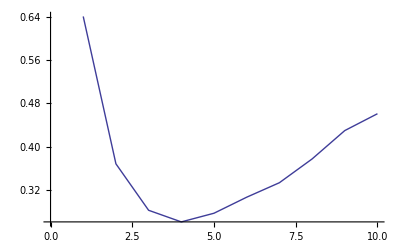

-Graphics-

```mathematica
clustering1000Fixed=Map[GlobalClusteringCoefficient,networks1000Fixed];
ListPlot[clustering1000Fixed,Joined->True]
apl1000Fixed=Map[MeanGraphDistance,networks1000Fixed];
ListPlot[apl1000Fixed]
```

## Capacidad distribuida uniformemente

```mathematica
networks100Uniform=Table[Import[StringJoin["graphs/model-v3/uniform-t1000-2/","network-100-",IntegerString[i],".graphml"]],{i,1,10,1}];
```

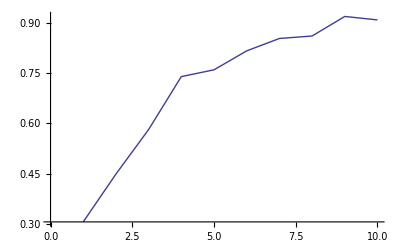

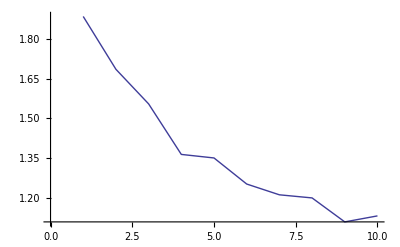

```mathematica
clustering100Uniform=Map[GlobalClusteringCoefficient,networks100Uniform];
apl100Uniform=Map[MeanGraphDistance,networks100Uniform];
ListPlot[clustering100Uniform,Joined->True]
ListPlot[apl100Uniform,Joined->True]
```

```mathematica
networks1000Uniform=Table[Import[StringJoin["graphs/model-v3/uniform-t1000-2/","network-1000-",IntegerString[i],".graphml"]],{i,1,10,1}];
```

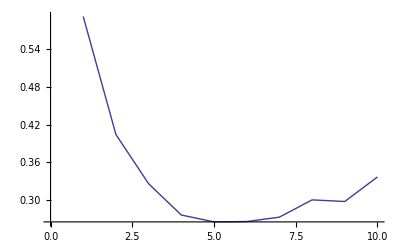

-Graphics-

```mathematica
clustering1000Uniform=Map[GlobalClusteringCoefficient,networks1000Uniform];
apl1000Uniform=Map[MeanGraphDistance,networks1000Uniform];
ListPlot[clustering1000Uniform,Joined->True]
ListPlot[apl1000Uniform,Joined->True]
```

## Capacidad distribuida normal con desviación=3

```mathematica
networks100Normal=Table[Import[StringJoin["graphs/model-v3/normal-t1000-2/","network-100-",IntegerString[i],".graphml"]],{i,1,10,1}];
```

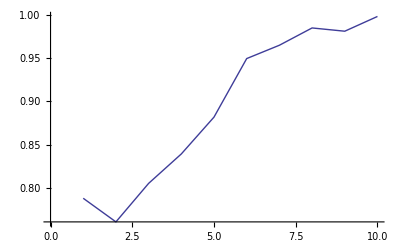

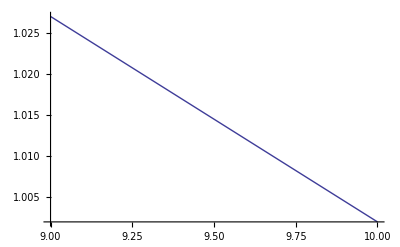

```mathematica
clustering100Normal=Map[GlobalClusteringCoefficient,networks100Normal];
apl100Normal=Map[MeanGraphDistance,networks100Normal];
ListPlot[clustering100Normal,Joined->True]
ListPlot[apl100Normal,Joined->True]
```

```mathematica
networks1000Normal=Table[Import[StringJoin["graphs/model-v3/normal-t1000-2/","network-1000-",IntegerString[i],".graphml"]],{i,1,10,1}];
```

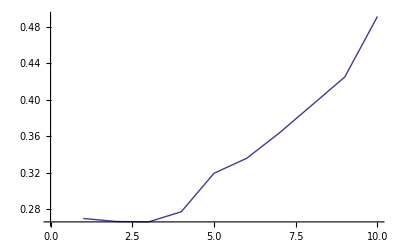

-Graphics-

```mathematica
clustering1000Normal=Map[GlobalClusteringCoefficient,networks1000Normal];
apl1000Normal=Map[MeanGraphDistance,networks1000Normal];
ListPlot[clustering1000Normal,Joined->True]
ListPlot[apl1000Normal,Joined->True]
```

## Capacidad distribuida normal con desviación=3

```mathematica
networks100Normal=Table[Import[StringJoin["graphs/model-v3/normal-t1000-2/","network-100-",IntegerString[i],".graphml"]],{i,1,10,1}];
```

```mathematica
clustering100Normal=Map[GlobalClusteringCoefficient,networks100Normal];
apl100Normal=Map[MeanGraphDistance,networks100Normal];
ListPlot[clustering100Normal,Joined->True]
ListPlot[apl100Normal,Joined->True]
```

-Graphics-

-Graphics-

```mathematica
networks1000Normal=Table[Import[StringJoin["graphs/model-v3/normal-t1000-2/","network-1000-",IntegerString[i],".graphml"]],{i,1,10,1}];
```

```mathematica
clustering1000Normal=Map[GlobalClusteringCoefficient,networks1000Normal];
apl1000Normal=Map[MeanGraphDistance,networks1000Normal];
ListPlot[clustering1000Normal,Joined->True]
ListPlot[apl1000Normal,Joined->True]
```

-Graphics-

-Graphics-

# Modelo versión 3

Lim-capacity: [1-10] --> 1
10.000 unidades de tiempo

## Capacidad fija

```mathematica
networks100Fixed=Table[Import[StringJoin["graphs/model-v3/fixed10mil/","network-100-",IntegerString[i],".graphml"]],{i,1,10,1}];
```

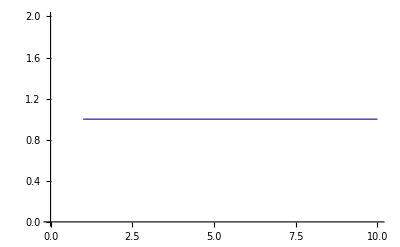

-Graphics-

```mathematica
clustering100Fixed=Map[GlobalClusteringCoefficient,networks100Fixed];
apl100Fixed=Map[MeanGraphDistance,networks100Fixed];
ListPlot[clustering100Fixed,Joined->True]
ListPlot[apl100Fixed,Joined->True]
```

```mathematica
vals={1,5,10};
networks1000Fixed=Table[Import[StringJoin["graphs/model-v3/fixed-t1000-2/","network-1000-",IntegerString[vals[[i]]],".graphml"]],{i,1,3,1}];
```

{1329/2072,89047/322292,7780395/16879348}

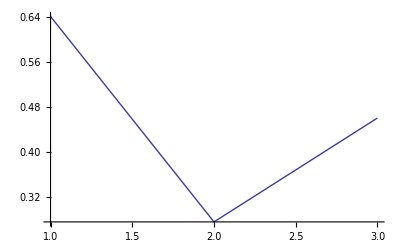

{∞,∞,∞}

-Graphics-

```mathematica
clustering1000Fixed=Map[GlobalClusteringCoefficient,networks1000Fixed]
ListPlot[clustering1000Fixed,Joined->True]
apl1000Fixed=Map[MeanGraphDistance,networks1000Fixed]
ListPlot[apl1000Fixed]
```

## Capacidad distribuida uniformemente

```mathematica
networks100Uniform=Table[Import[StringJoin["graphs/model-v3/uniform10mil/","network-100-",IntegerString[i],".graphml"]],{i,1,10,1}];
```

```mathematica
clustering100Uniform=Map[GlobalClusteringCoefficient,networks100Uniform];
apl100Uniform=Map[MeanGraphDistance,networks100Uniform];
ListPlot[clustering100Uniform,Joined->True]
ListPlot[apl100Uniform,Joined->True]
```

-Graphics-

-Graphics-

```mathematica
vals={1,5,10};
networks1000Uniform=Table[Import[StringJoin["graphs/model-v3/uniform-t1000-2/","network-1000-",IntegerString[vals[[i]]],".graphml"]],{i,1,3,1}];
```

{2649/4480,86679/326281,563487/1672360}

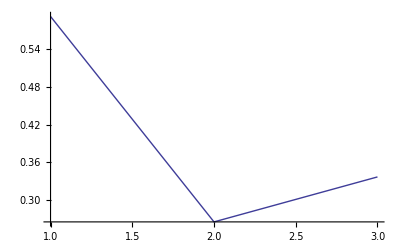

{∞,∞,∞}

-Graphics-

```mathematica
clustering1000Uniform=Map[GlobalClusteringCoefficient,networks1000Uniform]
ListPlot[clustering1000Uniform,Joined->True]
apl1000Uniform=Map[MeanGraphDistance,networks1000Uniform]
ListPlot[apl1000Uniform,Joined->True]
```

## Capacidad distribuida normal con desviación=3

```mathematica
networks100Normal=Table[Import[StringJoin["graphs/model-v3/normalt10mil/","network-100-",IntegerString[i],".graphml"]],{i,1,10,1}];
```

```mathematica
clustering100Normal=Map[GlobalClusteringCoefficient,networks100Normal];
apl100Normal=Map[MeanGraphDistance,networks100Normal];
ListPlot[clustering100Normal,Joined->True]
ListPlot[apl100Normal,Joined->True]
```

-Graphics-

-Graphics-

```mathematica
vals={1,5,10};
networks1000Normal=Table[Import[StringJoin["graphs/model-v3/normal-t1000-2/","network-1000-",IntegerString[vals[[i]]],".graphml"]],{i,1,3,1}];
```

{2109/7825,542250/1698793,7862859/15994898}

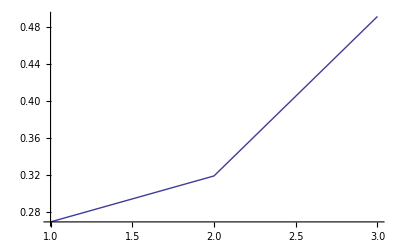

{∞,∞,∞}

-Graphics-

```mathematica
clustering1000Normal=Map[GlobalClusteringCoefficient,networks1000Normal]
ListPlot[clustering1000Normal,Joined->True]
apl1000Normal=Map[MeanGraphDistance,networks1000Normal]
ListPlot[apl1000Normal,Joined->True]
```

Lim-capacity: [1-10] --> 1
100.000 unidades de tiempo

## Capacidad fija

```mathematica
networks100Fixed=Table[Import[StringJoin["graphs/model-v3/fixed100mil/","network-100-",IntegerString[i],".graphml"]],{i,1,10,1}];
```

```mathematica
clustering100Fixed=Map[GlobalClusteringCoefficient,networks100Fixed];
apl100Fixed=Map[MeanGraphDistance,networks100Fixed];
ListPlot[clustering100Fixed,Joined->True]
ListPlot[apl100Fixed,Joined->True]
```

-Graphics-

-Graphics-

## Capacidad distribuida uniformemente

```mathematica
networks100Uniform=Table[Import[StringJoin["graphs/model-v3/uniform100mil/","network-100-",IntegerString[i],".graphml"]],{i,1,10,1}];
```

```mathematica
clustering100Uniform=Map[GlobalClusteringCoefficient,networks100Uniform];
apl100Uniform=Map[MeanGraphDistance,networks100Uniform];
ListPlot[clustering100Uniform,Joined->True]
ListPlot[apl100Uniform,Joined->True]
```

-Graphics-

## Capacidad distribuida normal con desviación=3

```mathematica
networks100Normal=Table[Import[StringJoin["graphs/model-v3/normalt100mil/","network-100-",IntegerString[i],".graphml"]],{i,1,10,1}];
```

-Graphics-

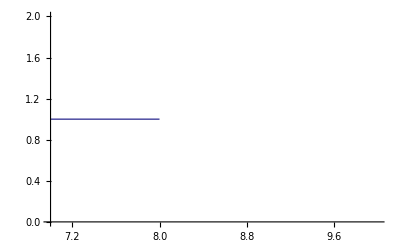

```mathematica
clustering100Normal=Map[GlobalClusteringCoefficient,networks100Normal];
apl100Normal=Map[MeanGraphDistance,networks100Normal];
ListPlot[clustering100Normal,Joined->True]
ListPlot[apl100Normal,Joined->True]
```